```mathematica
(*inner3D computes the inner 2 integrals for the 3D FT in spherical coords*)
```

```mathematica
inner3D := 2 Pi Integrate[Exp[-2 Pi I k r Cos[θ]]*Sin[θ],{θ,0,Pi}]
```

```mathematica
(*We can compute the FT of 1/r in this way*)
```

```mathematica
G=Limit[Assuming[{b>0, k>0},Integrate[Exp[-b r]/r inner3D r^2, {r,0,Infinity}]],b->0]
```

1/(k^2 π)

```mathematica
(*The FT of our de-sing kernel doesn't formally converge, but IBP of it does (the endpoints eval part ends up being 0 to satisfy that the result recovers FT of 1/r)*)
```

```mathematica
ibp = Simplify[D[r/Sqrt[r^2+a^2],r]]*Integrate[r inner3D,r]
```

-(a^2 Cos[2 k π r])/(k^2 π (a^2+r^2)^(3/2))

```mathematica
(*The FT of our de-sing kernel*)
```

```mathematica
ft3d1 = Assuming[{a>0, k>0},Integrate[-ibp, {r,0,Infinity}]]
```

(2 a BesselK[1,2 a k π])/k

```mathematica
(*Inverse FT recovers original de-sing kernel*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[ft3d1 inner3D k^2,{k,0,Infinity}]]
```

1/(√(a^2+r^2))

```mathematica
Limit[ft3d1,a->0]
```

1/(k^2 π)

```mathematica
(*We can use same process to calc FT of "high-order" de-sing kernels from vortex literature*)
```

```mathematica
ibp2 = Simplify[D[r(r^2+3/2a^2)/(r^2+a^2)^(3/2),r]]*Integrate[r inner3D,r]
```

-(3 a^4 Cos[2 k π r])/(2 k^2 π (a^2+r^2)^(5/2))

```mathematica
ft3d4 = Assuming[{a>0, k>0},Integrate[-ibp2, {r,0,Infinity}]]
```

2 a^2 π BesselK[2,2 a k π]

```mathematica
(*Verify that the IFT recovers our original de-sing kernel*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[ft3d4 inner3D k^2,{k,0,Infinity}]]
```

(3 a^2+2 r^2)/(2 (a^2+r^2)^(3/2))

```mathematica
(*Looking at the FT of the HO kernel, we notice a pattern of a^n k^(n-2) π^(n-1) BesselK[n,2 a k π] for n=1 and 2, what about n=3?*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[a^3 k^1 π^2 BesselK[3,2 a k π] inner3D k^2,{k,0,Infinity}]]
```

(15 a^4+20 a^2 r^2+8 r^4)/(8 (a^2+r^2)^(5/2))

```mathematica
(*We can make a function to generate an arbitrary n-th version. Note that we need the coefficient on the highest power of 'r' to be 1, so that when a=0 we recover 1/r. Inspection tells us that we need to multiply the IFT of our pattern by (2/(n-1)!) to get the coefficient to be 1*)
```

```mathematica
DeSingKernel[n_]:= (2/(n-1)!)*Assuming[{a>0, r>0},Integrate[a^n k^(n-2) π^(n-1) BesselK[n,2 a k π] inner3D k^2,{k,0,Infinity}]]
```

```mathematica
(*Alternate approach to computing FT of de-sing kernel that I'm not sure quite works*)
```

```mathematica
inner3Dexp=Expand[TrigToExp[inner3D]*Exp[-b r]]
```

(ⅈ ⅇ^(-b r-2 ⅈ k π r))/(k r)-(ⅈ ⅇ^(-b r+2 ⅈ k π r))/(k r)

```mathematica
ft3d2 = Limit[Assuming[{k>0, a>0, b>0},Integrate[(1/Sqrt[r^2+a^2])inner3Dexp r^2,{r,0,Infinity}]],b->0]
```

(4+ⅈ a k π^2 BesselY[1,-2 ⅈ a k π]-ⅈ a k π^2 BesselY[1,2 ⅈ a k π])/(2 k^2 π)

```mathematica
ft3d3 = Limit[Assuming[{k>0, a>0, b>0},Integrate[((r^2+3/2a^2)/(r^2+a^2)^(3/2))inner3Dexp r^2,{r,0,Infinity}]],b->0]
```

-3/2 a^2 π^2 (BesselY[0,-2 ⅈ a k π]+BesselY[0,2 ⅈ a k π])

```mathematica
s[n_]:=Apart[(-d)^n D[1/Sqrt[r^2+a^2],{a,n}]/n!/.a->d,r]
```

```mathematica
s2[n_]:=Apart[(-d)^n D[(r^2+3/2a^2)/(r^2+a^2)^(3/2),{a,n}]/n!/.a->d,r]
```

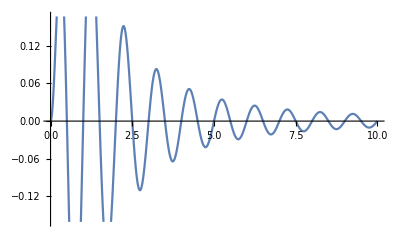

```mathematica
Plot[(1r/(r^2+1^2)^(3/2))*Sin[2 Pi 1r],{r,0,10}]
```

```mathematica
FT[x_]:=Assuming[{d>0, k>0},Integrate[x inner3D r^2 ,{r,0,Infinity}]]
```

```mathematica
Fdesing[n_,m_]:=Total[FT[List@@Apart[Normal[Series[DeSingKernel[n],{a,d,m}]]/.a->0,r][[1;;-(n+1)]]]] + ((2/(n-1)!)d^n k^(n-2) π^(n-1) BesselK[n,2 d k π])
```

```mathematica
Fs[n_]:=Total[F[Coefficient[s[n],d,Range[2n]]]*d^Range[2n]]
```

```mathematica
Fs2[n_]:=Total[F[Coefficient[s2[n],d,Range[2n+2]]]*d^Range[2n+2]]
```

```mathematica
fs0 = ft3d1/.a->d
```

(2 d BesselK[1,2 d k π])/k

```mathematica
fs1=Fs[1]
```

4 d^2 π BesselK[0,2 d k π]

```mathematica
fs2=Fs[2]
```

-2 d^2 π BesselK[0,2 d k π]+4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs3=Fs[3]
```

-4 d^3 k π^2 BesselK[1,2 d k π]+8/3 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
fs4=Fs[4]
```

d^3 k π^2 BesselK[1,2 d k π]-4 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
fs5=Fs[5]
```

2 d^4 k^2 π^3 BesselK[2,2 d k π]-8/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
fs20=ft3d4/.a->d
```

2 d^2 π BesselK[2,2 d k π]

```mathematica
fs21=Fs2[1]
```

4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs22=Fs2[2]
```

-6 d^3 k π^2 BesselK[1,2 d k π]+4 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
fs23=Fs2[3]
```

4 d^3 k π^2 BesselK[1,2 d k π]-28/3 d^4 k^2 π^3 BesselK[2,2 d k π]+8/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
fs24=Fs2[4]
```

-d^3 k π^2 BesselK[1,2 d k π]+9 d^4 k^2 π^3 BesselK[2,2 d k π]-8 d^5 k^3 π^4 BesselK[3,2 d k π]+4/3 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
fs25=Fs2[5]
```

-4 d^4 k^2 π^3 BesselK[2,2 d k π]+10 d^5 k^3 π^4 BesselK[3,2 d k π]-24/5 d^6 k^4 π^5 BesselK[4,2 d k π]+8/15 d^7 k^5 π^6 BesselK[5,2 d k π]

```mathematica
T=Accumulate[{fs0,fs1,fs2,fs3,fs4,fs5}]
```

{(2 d BesselK[1,2 d k π])/k,4 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k,2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+4 d^3 k π^2 BesselK[1,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+8/3 d^4 k^2 π^3 BesselK[2,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π],fs5+2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]}

```mathematica
T2=Accumulate[{fs20,fs21,fs22,fs23,fs24,fs25}]
```

{2 d^2 π BesselK[2,2 d k π],4 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π],-2 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]+4 d^4 k^2 π^3 BesselK[2,2 d k π],2 d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]-16/3 d^4 k^2 π^3 BesselK[2,2 d k π]+8/3 d^5 k^3 π^4 BesselK[3,2 d k π],d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]+11/3 d^4 k^2 π^3 BesselK[2,2 d k π]-16/3 d^5 k^3 π^4 BesselK[3,2 d k π]+4/3 d^6 k^4 π^5 BesselK[4,2 d k π],d^3 k π^2 BesselK[1,2 d k π]+2 d^2 π BesselK[2,2 d k π]-1/3 d^4 k^2 π^3 BesselK[2,2 d k π]+14/3 d^5 k^3 π^4 BesselK[3,2 d k π]-52/15 d^6 k^4 π^5 BesselK[4,2 d k π]+8/15 d^7 k^5 π^6 BesselK[5,2 d k π]}

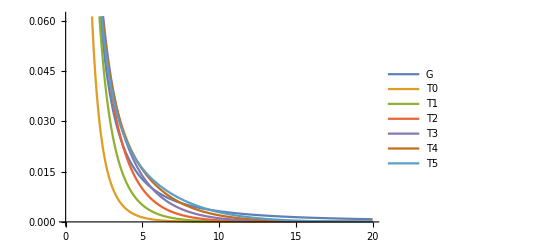

```mathematica
Plot[Evaluate@({G,T}/.d->0.1),{k,0,20},PlotLegends->{"G","T0","T1","T2","T3","T4","T5"}]
```

```mathematica
Assuming[d>0,Integrate[(G-T[[6]])^2,{k,0,Infinity}]]
```

(3059 d^3 π^3)/1048576

```mathematica
Assuming[d>0,Integrate[(G-T2[[6]])^2,{k,0,Infinity}]]
```

(49021 d^3 π^3)/33554432

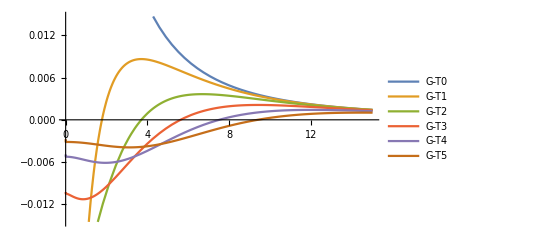

```mathematica
Plot[Evaluate@(G-T/.d->0.1),{k,0,15},PlotLegends->{"G-T0","G-T1","G-T2","G-T3","G-T4","G-T5"}]
```

```mathematica
Assuming[{k>=0},Series[T[[6]],{d,0,5}]]
```

1/(k^2 π)+(π d^2)/10+1/20 k^2 π^3 d^4+O[d]^6

```mathematica
Assuming[{k>=0},Series[T2[[6]],{d,0,5}]]
```

1/(k^2 π)-1/20 (k^2 π^3) d^4+O[d]^6

```mathematica
u=Sin[Pi x]Sin[Pi y]Sin[Pi z]/(-3 Pi^2)
```

-(Sin[π x] Sin[π y] Sin[π z])/(3 π^2)

```mathematica
ff=Laplacian[u,{x,y,z}]
```

Sin[π x] Sin[π y] Sin[π z]

```mathematica
t=Normal[Series[1/Sqrt[r^2 + a^2],{a,d,3}]]/.a->0
```

(d^2 (2 d^2-r^2))/(2 (d^2+r^2)^(5/2))+d^2/((d^2+r^2)^(3/2))+1/(√(d^2+r^2))-(d^3 (-2 d^3+3 d r^2))/(2 (d^2+r^2)^(7/2))

```mathematica
FortranForm[Simplify[t]]
```

(8*d**6 + 8*d**4*r**2 + 7*d**2*r**4 + 2*r**6)/(2.*(d**2 + r**2)**3.5)

```mathematica
t2=Normal[Series[(3 a^2+2 r^2)/(2 (a^2+r^2)^(3/2)),{a,d,5}]]/.a->0
```

(3 d^4)/(2 (d^2+r^2)^(5/2))+(3 d^2+2 r^2)/(2 (d^2+r^2)^(3/2))+(3 d^2 (2 d^4-3 d^2 r^2))/(4 (d^2+r^2)^(7/2))+(d^4 (6 d^4-23 d^2 r^2+6 r^4))/(4 (d^2+r^2)^(9/2))+(3 d^6 (8 d^6-88 d^4 r^2+115 d^2 r^4-20 r^6))/(16 (d^2+r^2)^(13/2))+(3 d^4 (8 d^6-56 d^4 r^2+39 d^2 r^4-2 r^6))/(16 (d^2+r^2)^(11/2))

```mathematica
FortranForm[t2/.{d^2+r^2->k}]
```

(3*d**4)/(2.*k**2.5) + (3*d**2 + 2*r**2)/(2.*k**1.5) + (3*d**2*(2*d**4 - 3*d**2*r**2))/(4.*k**3.5) + (d**4*(6*d**4 - 23*d**2*r**2 + 6*r**4))/(4.*k**4.5) + 
     -  (3*d**6*(8*d**6 - 88*d**4*r**2 + 115*d**2*r**4 - 20*r**6))/(16.*k**6.5) + (3*d**4*(8*d**6 - 56*d**4*r**2 + 39*d**2*r**4 - 2*r**6))/(16.*k**5.5)

```mathematica
t2=Normal[Series[(3 a^2+2 r^2)/(2 (a^2+r^2)^(3/2)),{a,d,5}]]/.a->0
```